```mathematica
Table[
With[
{g=Graph[GraphFromSets[part],VertexLabels->"Name"]},
CompleteBaseCoeff[ ChromaticPolynomial[g,x]]
],{part,KSetPartitions[6,4]}]//Tally//Sort
```

{{{0,0,0,0,1,2,1},45},{{0,0,0,0,1,3,1},20}}

```mathematica
Table[
With[
{g=Graph[GraphFromSets[part],VertexLabels->"Name"]},
CompleteBaseCoeff[ ChromaticPolynomial[g,x]]
],{part,KSetPartitions[7,4]}]//Tally//Sort
```

{{{0,0,0,0,1,3,3,1},105},{{0,0,0,0,1,4,4,1},210},{{0,0,0,0,1,7,6,1},35}}

```mathematica
TableForm[Table[
With[
{g=Graph[GraphFromSets[part],VertexLabels->"Name"]},
CompleteBaseCoeff[ ChromaticPolynomial[g,x]]
],{part,KSetPartitions[8,4]}]//Tally//Sort,TableDepth->1]
```

{{0,0,0,0,1,4,6,4,1},105}
{{0,0,0,0,1,5,8,5,1},840}
{{0,0,0,0,1,6,11,6,1},280}
{{0,0,0,0,1,8,13,7,1},420}
{{0,0,0,0,1,15,25,10,1},56}

```mathematica
PartitionType[{{1},{2},{3,4},{5,6,7,8}}]
```

{4,2,1,1}

```mathematica
TableForm[Table[
PartitionType[part],{part,KSetPartitions[8,4]}]//Tally//Sort,TableDepth->1]
```

{{2,2,2,2},105}
{{3,2,2,1},840}
{{3,3,1,1},280}
{{4,2,1,1},420}
{{5,1,1,1},56}

```mathematica
Map[PartitionType[#]&,Select[KSetPartitions[8,4],
With[
{g=Graph[GraphFromSets[#],VertexLabels->"Name"]},
CompleteBaseCoeff[ ChromaticPolynomial[g,x]]=={0,0,0,0,1,8,13,7,1}
]&
]]//Tally//Sort
```

{{{4,2,1,1},420}}

```mathematica
TableForm[Table[
With[
{g=Graph[GraphFromSets[part],VertexLabels->"Name"]},
CompleteBaseCoeff[ ChromaticPolynomial[g,x]]
],{part,KSetPartitions[9,4]}]//Tally//Sort,TableDepth->1]
```

{{0,0,0,0,1,6,13,13,6,1},1260}
{{0,0,0,0,1,7,17,17,7,1},2520}
{{0,0,0,0,1,9,21,20,8,1},1890}
{{0,0,0,0,1,10,28,26,9,1},1260}
{{0,0,0,0,1,16,40,35,11,1},756}
{{0,0,0,0,1,31,90,65,15,1},84}

```mathematica
TableForm[Table[
PartitionType[part],{part,KSetPartitions[9,4]}]//Tally//Sort,TableDepth->1]
```

{{3,2,2,2},1260}
{{3,3,2,1},2520}
{{4,2,2,1},1890}
{{4,3,1,1},1260}
{{5,2,1,1},756}
{{6,1,1,1},84}

```mathematica
TableForm[Table[
PartitionType[part],{part,KSetPartitions[10,4]}]//Tally//Sort,TableDepth->1]
```

{{3,3,2,2},6300}
{{3,3,3,1},2800}
{{4,2,2,2},3150}
{{4,3,2,1},12600}
{{4,4,1,1},1575}
{{5,2,2,1},3780}
{{5,3,1,1},2520}
{{6,2,1,1},1260}
{{7,1,1,1},120}

```mathematica
PartitionToCompleteCoeff[part_]:=Block[
{g=Graph[GraphFromSets[part],VertexLabels->"Name"]},
CompleteBaseCoeff[ ChromaticPolynomial[g,x]]
]
```

```mathematica
PartitionToEmptyCoeff[part_]:=Block[
{g=Graph[GraphFromSets[part],VertexLabels->"Name"]},
NullBaseCoeff[ ChromaticPolynomial[g,x]]
]
```

```mathematica
PartitionToEmptyCoeff[part_]:=Block[
{g=Graph[GraphFromSets[part],VertexLabels->"Name"]},
NullBaseCoeff[ ChromaticPolynomial[g,x]]
]
```

```mathematica
TableForm[
Map[
{#[[1,1]],SetsToSymbol2[#[[1,2]]],PartitionToCompleteCoeff[#[[1,2]]],#[[2]]}&,

Sort[
Tally[
Table[
{PartitionType[part],part},{part,KSetPartitions[6,4]}],
#1[[1]]==#2[[1]]&
]
]
],TableDepth->1]
```

{{2,2,1,1},v1x2x34x56,{0,0,0,0,1,2,1},45}
{{3,1,1,1},v1x2x3x456,{0,0,0,0,1,3,1},20}

```mathematica
TableForm[
Map[
{#[[1,1]],SetsToSymbol2[#[[1,2]]],PartitionToCompleteCoeff[#[[1,2]]],#[[2]]}&,

Sort[
Tally[
Table[
{PartitionType[part],part},{part,KSetPartitions[9,4]}],
#1[[1]]==#2[[1]]&
]
]
],TableDepth->1]
```

{{3,2,2,2},v12x34x56x789,{0,0,0,0,1,6,13,13,6,1},1260}
{{3,3,2,1},v1x23x456x789,{0,0,0,0,1,7,17,17,7,1},2520}
{{4,2,2,1},v1x23x45x6789,{0,0,0,0,1,9,21,20,8,1},1890}
{{4,3,1,1},v1x2x345x6789,{0,0,0,0,1,10,28,26,9,1},1260}
{{5,2,1,1},v1x2x34x56789,{0,0,0,0,1,16,40,35,11,1},756}
{{6,1,1,1},v1x2x3x456789,{0,0,0,0,1,31,90,65,15,1},84}

```mathematica
TableForm[
Map[
{#[[1,1]],SetsToSymbol2[#[[1,2]]],
With[
{c=ChromaticPolynomial[Graph[GraphFromSets[#[[1,2]]],VertexLabels->"Name"],x]},
MatrixForm[
{
CompleteBaseCoeff[ c],
NullBaseCoeff[ c],
TreeBaseCoeff[ c],
JacobsthalBaseCoeff[c]
 }
]
]
}&,

Sort[
Tally[
Table[
{PartitionType[part],part},{part,KSetPartitions[10,4]}],
#1[[1]]==#2[[1]]&
]
]
],TableDepth->1]
```

{{3,3,2,2},v12x34x567x89a,(0 | 0 | 0 | 0 | 1 | 8 | 24 | 34 | 24 | 8 | 1
0 | -139494 | 409747 | -492786 | 324835 | -131175 | 34023 | -5720 | 606 | -37 | 1
0 | 0 | 13730 | -39175 | 45187 | -28114 | 10483 | -2430 | 346 | -28 | 1
0 | 0 | 0 | -330 | -330 | 20 | 256 | -206 | 73 | -13 | 1)}
{{3,3,3,1},v1x234x567x89a,(0 | 0 | 0 | 0 | 1 | 9 | 30 | 45 | 30 | 9 | 1
0 | -122190 | 360761 | -436905 | 290580 | -118650 | 31194 | -5331 | 576 | -36 | 1
0 | 0 | 11828 | -33966 | 39528 | -24879 | 9414 | -2223 | 324 | -27 | 1
0 | 0 | 0 | -276 | -277 | 25 | 211 | -175 | 64 | -12 | 1)}
{{4,2,2,2},v12x34x56x789a,(0 | 0 | 0 | 0 | 1 | 10 | 30 | 41 | 28 | 9 | 1
0 | -114966 | 341631 | -417102 | 279972 | -115429 | 30634 | -5279 | 574 | -36 | 1
0 | 0 | 10862 | -31523 | 37174 | -23748 | 9124 | -2185 | 322 | -27 | 1
0 | 0 | 0 | -236 | -236 | 40 | 173 | -159 | 62 | -12 | 1)}
{{4,3,2,1},v1x23x456x789a,(0 | 0 | 0 | 0 | 1 | 11 | 38 | 54 | 35 | 10 | 1
0 | -101502 | 302733 | -371555 | 251186 | -104544 | 28087 | -4916 | 545 | -35 | 1
0 | 0 | 9488 | -27630 | 32759 | -21098 | 8202 | -1997 | 301 | -26 | 1
0 | 0 | 0 | -204 | -204 | 32 | 149 | -136 | 54 | -11 | 1)}
{{4,4,1,1},v1x2x3456x789a,(0 | 0 | 0 | 0 | 1 | 14 | 61 | 86 | 50 | 12 | 1
0 | -76110 | 229289 | -285389 | 196558 | -83788 | 23196 | -4212 | 488 | -33 | 1
0 | 0 | 6902 | -20303 | 24442 | -16092 | 6450 | -1636 | 260 | -24 | 1
0 | 0 | 0 | -143 | -142 | 21 | 103 | -94 | 39 | -9 | 1)}
{{5,2,2,1},v1x23x45x6789a,(0 | 0 | 0 | 0 | 1 | 17 | 56 | 75 | 46 | 12 | 1
0 | -63198 | 194901 | -249495 | 177112 | -77795 | 22134 | -4111 | 484 | -33 | 1
0 | 0 | 5204 | -15978 | 20228 | -14034 | 5910 | -1563 | 256 | -24 | 1
0 | 0 | 0 | -76 | -76 | 43 | 40 | -65 | 35 | -9 | 1)}
{{5,3,1,1},v1x2x345x6789a,(0 | 0 | 0 | 0 | 1 | 18 | 71 | 100 | 56 | 13 | 1
0 | -57054 | 175957 | -225431 | 160408 | -70795 | 20308 | -3820 | 458 | -32 | 1
0 | 0 | 4718 | -14439 | 18230 | -12639 | 5340 | -1426 | 238 | -23 | 1
0 | 0 | 0 | -75 | -77 | 41 | 44 | -60 | 30 | -8 | 1)}
{{6,2,1,1},v1x2x34x56789a,(0 | 0 | 0 | 0 | 1 | 32 | 121 | 155 | 80 | 16 | 1
0 | -23118 | 76817 | -107667 | 84697 | -41599 | 13323 | -2799 | 374 | -29 | 1
0 | 0 | 1394 | -4847 | 7101 | -5783 | 2885 | -909 | 178 | -20 | 1
0 | 0 | 0 | -5 | -5 | 9 | -5 | -5 | 9 | -5 | 1)}
{{7,1,1,1},v1x2x3x456789a,(0 | 0 | 0 | 0 | 1 | 63 | 301 | 350 | 140 | 21 | 1
0 | -4374 | 16767 | -27702 | 26082 | -15498 | 6048 | -1554 | 254 | -24 | 1
0 | 0 | 128 | -576 | 1120 | -1232 | 840 | -364 | 98 | -15 | 1
0 | 0 | 0 | -5 | 4 | 40 | 10 | -10 | -6 | 0 | 1)}

```mathematica
TableForm[
Map[
{#[[1,1]],SetsToSymbol2[#[[1,2]]],PartitionToEmptyCoeff[#[[1,2]]],#[[2]]}&,

Sort[
Tally[
Table[
{PartitionType[part],part},{part,KSetPartitions[10,4]}],
#1[[1]]==#2[[1]]&
]
]
],TableDepth->1]
```

{{3,3,2,2},v12x34x567x89a,{0,-139494,409747,-492786,324835,-131175,34023,-5720,606,-37,1},6300}
{{3,3,3,1},v1x234x567x89a,{0,-122190,360761,-436905,290580,-118650,31194,-5331,576,-36,1},2800}
{{4,2,2,2},v12x34x56x789a,{0,-114966,341631,-417102,279972,-115429,30634,-5279,574,-36,1},3150}
{{4,3,2,1},v1x23x456x789a,{0,-101502,302733,-371555,251186,-104544,28087,-4916,545,-35,1},12600}
{{4,4,1,1},v1x2x3456x789a,{0,-76110,229289,-285389,196558,-83788,23196,-4212,488,-33,1},1575}
{{5,2,2,1},v1x23x45x6789a,{0,-63198,194901,-249495,177112,-77795,22134,-4111,484,-33,1},3780}
{{5,3,1,1},v1x2x345x6789a,{0,-57054,175957,-225431,160408,-70795,20308,-3820,458,-32,1},2520}
{{6,2,1,1},v1x2x34x56789a,{0,-23118,76817,-107667,84697,-41599,13323,-2799,374,-29,1},1260}
{{7,1,1,1},v1x2x3x456789a,{0,-4374,16767,-27702,26082,-15498,6048,-1554,254,-24,1},120}

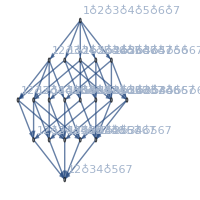
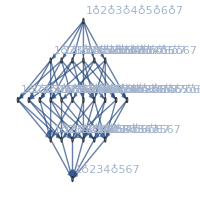
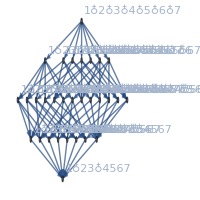
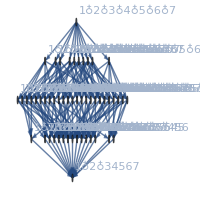
{{3,2,2},v12x34x567,6,-Graphics-,{0,0,0,1,5,8,5,1},105}
{{3,3,1},v1x234x567,7,-Graphics-,{0,0,0,1,6,11,6,1},70}
{{4,2,1},v1x23x4567,9,-Graphics-,{0,0,0,1,8,13,7,1},105}
{{5,1,1},v1x2x34567,16,-Graphics-,{0,0,0,1,15,25,10,1},21}

```mathematica
TableForm[
Map[
With[{g=Graph[GraphFromSets[#[[1,2]]],VertexLabels->"Name"]},
{#[[1,1]],SetsToSymbol2[#[[1,2]]],ChromaticPolynomial[g,4]/24,FormulaGraph[ FindFullFormula[g]],CompleteBaseCoeff[ChromaticPolynomial[g,x]],#[[2]]}
]&,

Sort[
Tally[
Table[
{PartitionType[part],part},{part,KSetPartitions[7,3]}],
#1[[1]]==#2[[1]]&
]
]
],TableDepth->1]
```

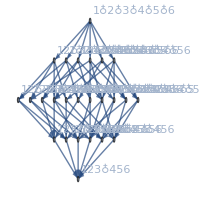
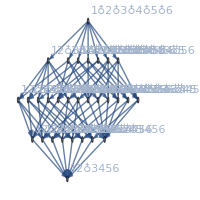
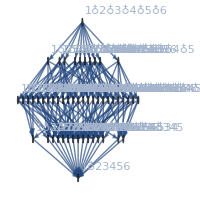
{{3,3},v123x456,35/2,-Graphics-,{0,0,1,6,11,6,1},10}
{{4,2},v12x3456,43/2,-Graphics-,{0,0,1,8,13,7,1},15}
{{5,1},v1x23456,81/2,-Graphics-,{0,0,1,15,25,10,1},6}

```mathematica
TableForm[
Map[
With[{g=Graph[GraphFromSets[#[[1,2]]],VertexLabels->"Name"]},
{#[[1,1]],SetsToSymbol2[#[[1,2]]],ChromaticPolynomial[g,4]/24,FormulaGraph[ FindFullFormula[g]],CompleteBaseCoeff[ChromaticPolynomial[g,x]],#[[2]]}
]&,

Sort[
Tally[
Table[
{PartitionType[part],part},{part,KSetPartitions[6,2]}],
#1[[1]]==#2[[1]]&
]
]
],TableDepth->1]
```

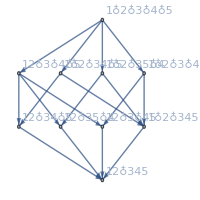
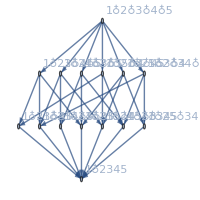
{{3,2},v12x345,17/2,-Graphics-,{0,0,1,4,4,1},10}
{{4,1},v1x2345,27/2,-Graphics-,{0,0,1,7,6,1},5}

```mathematica
TableForm[
Map[
With[{g=Graph[GraphFromSets[#[[1,2]]],VertexLabels->"Name"]},
{#[[1,1]],SetsToSymbol2[#[[1,2]]],ChromaticPolynomial[g,4]/24,FormulaGraph[ FindFullFormula[g]],CompleteBaseCoeff[ChromaticPolynomial[g,x]],#[[2]]}
]&,

Sort[
Tally[
Table[
{PartitionType[part],part},{part,KSetPartitions[5,2]}],
#1[[1]]==#2[[1]]&
]
]
],TableDepth->1]
```

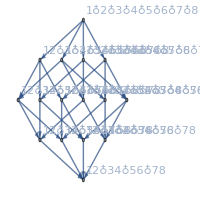
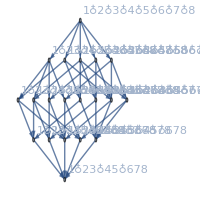
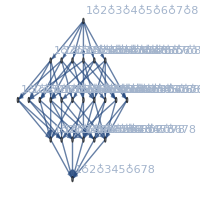
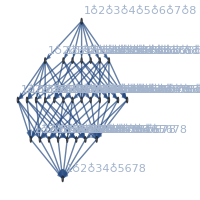
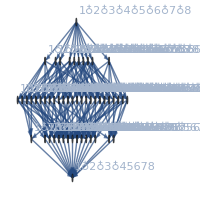
{{2,2,2,2},v12x34x56x78,5,-Graphics-,{0,0,0,0,1,4,6,4,1},105}
{{3,2,2,1},v1x23x45x678,6,-Graphics-,{0,0,0,0,1,5,8,5,1},840}
{{3,3,1,1},v1x2x345x678,7,-Graphics-,{0,0,0,0,1,6,11,6,1},280}
{{4,2,1,1},v1x2x34x5678,9,-Graphics-,{0,0,0,0,1,8,13,7,1},420}
{{5,1,1,1},v1x2x3x45678,16,-Graphics-,{0,0,0,0,1,15,25,10,1},56}

```mathematica
TableForm[
Map[
With[{g=Graph[GraphFromSets[#[[1,2]]],VertexLabels->"Name"]},
{#[[1,1]],SetsToSymbol2[#[[1,2]]],ChromaticPolynomial[g,5]/120,FormulaGraph[ FindFullFormula[g]],CompleteBaseCoeff[ChromaticPolynomial[g,x]],#[[2]]}
]&,

Sort[
Tally[
Table[
{PartitionType[part],part},{part,KSetPartitions[8,4]}],
#1[[1]]==#2[[1]]&
]
]
],TableDepth->1]
```

```mathematica
Log[2,64]
```

6

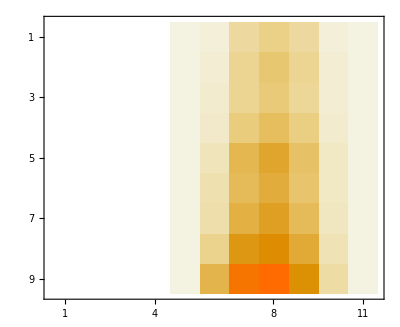

```mathematica
MatrixPlot[
Map[
PartitionToCompleteCoeff[#[[1,2]]]&,

Sort[
Tally[
Table[
{PartitionType[part],part},{part,KSetPartitions[10,4]}],
#1[[1]]==#2[[1]]&
]
]
]]
```

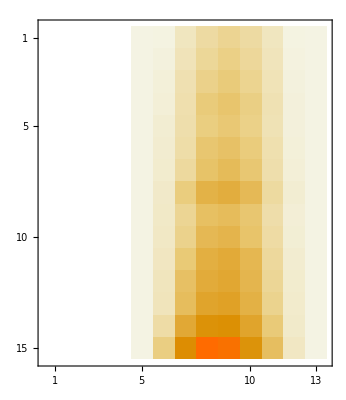

```mathematica
MatrixPlot[
Map[
PartitionToCompleteCoeff[#[[1,2]]]&,

Sort[
Tally[
Table[
{PartitionType[part],part},{part,KSetPartitions[12,4]}],
#1[[1]]==#2[[1]]&
]
]
]]
```